```mathematica
{ρ1,ρ2,d0,L1,L2,L3,μ1,H2,H1,g}={998,1.17,0.062,0.453,0.24,0.3,0.001,0.523,0.07,9.8};
(*{液体密度,空气密度,管1直径,管2直径,管3直径,瓶子直径,管1长度,管2长度,管3长度,液体动力粘度,大高度,小高度,重力加速度}*)
s3=1/4 π d^2 ;    (*管3截面积*)
s2=1/4 π d^2 ;    (*管2截面积*)
s1=1/4 π d^2 ;    (*管1截面积*)
s0=1/4 π d0^2 ;    (*瓶子截面积*)

v1=v3*d^2/d^2 ;    (*管1速度*)
v2=v3*d^2/d^2 ;    (*管2速度*)
v4=v3*d^2/d0^2  ;    (*瓶内液面速度*)
Re1=(ρ1 d v1)/μ1 ;    (*管1雷诺数*)
Re3=(ρ1 d v3)/μ1 ;     (*管3雷诺数*)

hf1=1/2*(1-s1/s0)*v1^2/2+0.0424*L1/d*v1^2/2  ;    (*管1入口与流动损耗*)
hf2=1/2*(1-s2/s0)*v2^2/2+(1-s2/s0)^2*v2^2/2 ;     (*空气出入损耗*)

hf3=1/2*(1-s3/s0)*v3^2/2+0.0424*L3/d*v3^2/2 +(1-s3/∞)^2*v3^2/2 ;     (*管3出入,流动损耗*)
hf4=v1^2/2-v4^2/2(*管1出与传递损耗*);
Eqn=ρ1*g*(H2-H1)==ρ1*hf1+ρ2*hf2+ρ1*hf3+ρ1*hf4+1/2 ρ1*v3^2;
Sol=Solve[Eqn,v3];
vout=v3/.Sol[[2]];
H0=(1000*vout^2)/(2*g)
Plot[H0,{d,0.0025,0.007}]
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

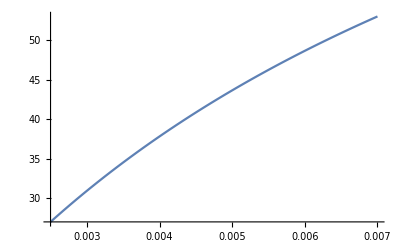

```mathematica
3.934849056590592*10^21./(3.4760078864138777*10^19 + 2.7732607682026298*10^17./x - 2.2663004843867187*10^21*x.^2 - 5.871562332031251*10^23*x.^4)
```